```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];SetDirectory[NotebookDirectory[]];
```

## 1. Set up parameters

### 1.1 read input parameters H_0, Ω_b0, Ω_c0, T_CMB, n_s, α, q_0, (Ṽ)_1

```mathematica
inputdata=Import["GR_input_data.txt","Table"]
```

{{70},{0.05},{0.25},{2.7},{1.},{-1.1},{-0.5}}

```mathematica
{inputH0,inputOmb0,inputOmc0,inputTcmb,inputns}={inputdata[[1]][[1]],inputdata[[2]][[1]],inputdata[[3]][[1]],inputdata[[4]][[1]],inputdata[[5]][[1]]};
```

### 1.2 constants and derived quantities

```mathematica
n=4;coord={et,r,th,ph};ccoord={et,x,y,z};
```

```mathematica
mesi=9.1093837015*10^-31;mpsi=1.67262192369*10^-27;mhsi=1.673575*10^-27;Gconsi=6.67430*10^-11;cconsi=299792458;kbconsi=1.380649*10^-23;hconsi=6.62607015*10^-34;econsi=1.602176634*10^-19;ep0consi=8.85418782*10^-12;
```

```mathematica
hbarconsi=hconsi/(2*Pi);alconsi=econsi^2/(4*Pi*ep0consi*hbarconsi*cconsi);hye0si=mesi/(2*hbarconsi^2)*(econsi^2/(4*Pi*ep0consi))^2;sitsi=(8*Pi)/3*(econsi^2/(4*Pi*ep0consi*mesi*cconsi^2))^2;sisbsi=(Pi^2*kbconsi^4)/(60*hbarconsi^3*cconsi^2);
```

```mathematica
megeo=(Gconsi*mesi)/cconsi^2;mpgeo=(Gconsi*mpsi)/cconsi^2;mhgeo=(Gconsi*mhsi)/cconsi^2;sitgeo=sitsi;
```

```mathematica
pgnum1=15;pgnum2=10;pgnum3=8;zeronum=10^-80;errornum1=10^-3;errornum2=10^-2;errornum3=10^-9;
```

```mathematica
H0si=inputH0*1000/(3.08567758128*10^16*10^6);Tcmb=inputTcmb;Omb0num=inputOmb0;Omc0num=inputOmc0;Omga0num=(8*Pi*Gconsi)/(3*H0si^2*cconsi^2)*(8*Pi^5*kbconsi^4)/(15*hconsi^3*cconsi^3)*(Tcmb)^4;Omla0num=1-Omb0num-Omc0num-Omga0num;{Omga0num,Omla0num}
```

{0.0000486065,0.699951}

```mathematica
H0geo=H0si*1/cconsi;menum=megeo*H0geo;mpnum=mpgeo*H0geo;mhnum=mhgeo*H0geo;sitnum=sitsi*H0geo^2
```

3.80922×10^-81

```mathematica
nsnum=inputns;decalrsq=k^(nsnum-1);
```

```mathematica
kanum=8*Pi;H0num=1;{lnaini,lnaend}={-14,0};aininum=N[Exp[lnaini]];numrep0={H0->H0num,ka->kanum,Omb0->Omb0num,Omc0->Omc0num,Omga0->Omga0num,Omla0->Omla0num};
```

## 2. Calculate field equation

### 2.1 curvature quantities

```mathematica
scalarpertfuns={bps[et,x,y,z]->bps[et]*Exp[I*(kx*x+ky*y+kz*z)],bph[et,x,y,z]->bph[et]*Exp[I*(kx*x+ky*y+kz*z)],deugax[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deugay[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deugaz[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],bpigaxx[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z],bpigayy[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z],bpigazz[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x],bpigaxy[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,y],bpigaxz[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,z],bpigayz[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,y],deepga[et,x,y,z]->4*epga[et]*bth0[et]*Exp[I*(kx*x+ky*y+kz*z)],deubx[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deuby[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deubz[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],deepb[et,x,y,z]->epb[et]*deb[et]*Exp[I*(kx*x+ky*y+kz*z)],deucx[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deucy[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deucz[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],deepc[et,x,y,z]->epc[et]*dec[et]*Exp[I*(kx*x+ky*y+kz*z)],debt[et,x,y,z]->debt[et]*Exp[I*(kx*x+ky*y+kz*z)],debx[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],x],deby[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],y],debz[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],z]};
```

```mathematica
metric1=(af[et])^2*{{0,0,0,0},{0,1/(1+Omk0*H0^2*r^2),0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};metricet={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};metricetsph={{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};ctran={et,r*Sin[th]*Cos[ph],r*Sin[th]*Sin[ph],r*Cos[th]};jmet=Table[D[ctran[[i]],coord[[j]]],{i,1,n},{j,1,n}];jmetinv=Simplify[Inverse[jmet]];cmetric1=Simplify[Transpose[jmetinv].metric1.jmetinv/.{Cos[th]->z/r,Sin[th]->Sqrt[x^2+y^2]/r,Cos[ph]->x/Sqrt[x^2+y^2],Sin[ph]->y/Sqrt[x^2+y^2]}/.r->Sqrt[x^2+y^2+z^2]];cmetric=af[et]^2*(1+po*2*bps[et,x,y,z])*{{-1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+(1-po*2*bph[et,x,y,z])*cmetric1/.Omk0->0/.scalarpertfuns;
```

```mathematica
AbsoluteTiming[poord=1;inversecmetric=Normal[Series[Inverse[cmetric],{po,0,poord}]];chris=Normal[Series[Table[(1/2)*Sum[inversecmetric[[i,s]]*(D[cmetric[[s,k]],ccoord[[j]]]+D[cmetric[[j,s]],ccoord[[k]]]-D[cmetric[[j,k]],ccoord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}],{po,0,poord}]];riemann=Normal[Series[Table[D[chris[[i,j,ll]],ccoord[[k]]]-D[chris[[i,j,k]],ccoord[[ll]]]+Sum[chris[[i,k,s]]*chris[[s,ll,j]]-chris[[i,ll,s]]*chris[[s,k,j]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{ll,1,n}],{po,0,poord}]];ricci=Table[Sum[riemann[[s,j,s,k]],{s,1,n}],{j,1,n},{k,1,n}];riccis=Normal[Series[Sum[inversecmetric[[i,j]]*ricci[[i,j]],{i,1,n},{j,1,n}],{po,0,poord}]];einstein=Normal[Series[Table[ricci[[i,j]]-1/2*cmetric[[i,j]]*riccis,{i,1,n},{j,1,n}],{po,0,poord}]];]
```

{0.655282,Null}

### 2.2 bumblebee contribution

```mathematica
AbsoluteTiming[bdown={af[et]*btf[et],0,0,0}+po*af[et]*{debt[et,x,y,z],debx[et,x,y,z],deby[et,x,y,z],debz[et,x,y,z]}/.scalarpertfuns;bsq=Normal[Series[Sum[inversecmetric[[i,j]]*bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}],{po,0,poord}]];bbdown=Table[bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}];db=Table[D[bdown[[j]],ccoord[[i]]]-Sum[chris[[s1,i,j]]*bdown[[s1]],{s1,1,n}],{i,1,n},{j,1,n}];bten=Table[db[[i,j]]-db[[j,i]],{i,1,n},{j,1,n}];dbb=Table[D[bbdown[[j,k]],ccoord[[i]]]-Sum[chris[[s1,i,j]]*bbdown[[s1,k]]+chris[[s1,i,k]]*bbdown[[j,s1]],{s1,1,n}],{i,1,n},{j,1,n},{k,1,n}];ddbb=Table[D[dbb[[i2,i3,i4]],ccoord[[i1]]]-Sum[chris[[s1,i1,i2]]*dbb[[s1,i3,i4]]+chris[[s1,i1,i3]]*dbb[[i2,s1,i4]]+chris[[s1,i1,i4]]*dbb[[i2,i3,s1]],{s1,1,n}],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}];tbdown=Normal[Series[Table[xi*(1/2*cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*bbdown[[s1,s2]]*ricci[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-Sum[inversecmetric[[s1,s2]]*bbdown[[i,s1]]*ricci[[j,s2]]+inversecmetric[[s1,s2]]*bbdown[[j,s1]]*ricci[[i,s2]],{s1,1,n},{s2,1,n}]+1/2*(Sum[inversecmetric[[s1,s2]]*ddbb[[s1,i,s2,j]]+inversecmetric[[s1,s2]]*ddbb[[s1,j,s2,i]]-inversecmetric[[s1,s2]]*ddbb[[s1,s2,i,j]],{s1,1,n},{s2,1,n}]-cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*ddbb[[s1,s2,s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]))+ka*(Sum[inversecmetric[[s1,s2]]*bten[[i,s1]]*bten[[j,s2]],{s1,1,n},{s2,1,n}]-1/4*cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*bten[[s1,s2]]*bten[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-bv*cmetric[[i,j]]+2*bbdown[[i,j]]*bvp)+xi2*(-bsq*einstein[[i,j]]-bdown[[i]]*bdown[[j]]*riccis+Sum[ddbb[[i,j,i1,i2]]*inversecmetric[[i1,i2]],{i1,1,n},{i2,1,n}]-cmetric[[i,j]]*Sum[ddbb[[i1,i2,i3,i4]]*inversecmetric[[i1,i2]]*inversecmetric[[i3,i4]],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}])/.{bv->v1*bsq,bvp->v1},{i,1,n},{j,1,n}],{po,0,poord}]];]
```

{6.95397,Null}

### 2.3 photon energy-momentum tensor

```mathematica
ugaup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deugax[et,x,y,z],deugay[et,x,y,z],deugaz[et,x,y,z]}/.scalarpertfuns;ugadown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ugaup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfgamn=Normal[Series[Table[(ep+p)*ugadown[[i]]*ugadown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epga[et]+po*deepga[et,x,y,z],p->1/3*(epga[et]+po*deepga[et,x,y,z])},{po,0,poord}]]+po*{{0,0,0,0},{0,bpigaxx[et,x,y,z],bpigaxy[et,x,y,z],bpigaxz[et,x,y,z]},{0,bpigaxy[et,x,y,z],bpigayy[et,x,y,z],bpigayz[et,x,y,z]},{0,bpigaxz[et,x,y,z],bpigayz[et,x,y,z],bpigazz[et,x,y,z]}}/.scalarpertfuns;tfgamnup=Normal[Series[Table[Sum[tfgamn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfgamncon=Normal[Series[Table[Sum[D[tfgamnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfgamnup[[i2,i]]+chris[[i,i1,i2]]*tfgamnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.4 baryon energy-momentum tensor

```mathematica
ubup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deubx[et,x,y,z],deuby[et,x,y,z],deubz[et,x,y,z]}/.scalarpertfuns;ubdown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ubup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfbmn=Normal[Series[Table[(ep+p)*ubdown[[i]]*ubdown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epb[et]+po*deepb[et,x,y,z],p->0},{po,0,poord}]]/.scalarpertfuns;tfbmnup=Normal[Series[Table[Sum[tfbmn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfbmncon=Normal[Series[Table[Sum[D[tfbmnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfbmnup[[i2,i]]+chris[[i,i1,i2]]*tfbmnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.5 cold dark matter energy-momentum tensor

```mathematica
ucup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deucx[et,x,y,z],deucy[et,x,y,z],deucz[et,x,y,z]}/.scalarpertfuns;ucdown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ucup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfcmn=Normal[Series[Table[(ep+p)*ucdown[[i]]*ucdown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epc[et]+po*deepc[et,x,y,z],p->0},{po,0,poord}]]/.scalarpertfuns;tfcmnup=Normal[Series[Table[Sum[tfcmn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfcmncon=Normal[Series[Table[Sum[D[tfcmnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfcmnup[[i2,i]]+chris[[i,i1,i2]]*tfcmnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.6 Einstein field equations

```mathematica
eeq=einstein-ka*tfgamn-ka*tfbmn-ka*tfcmn-tbdown+bla*cmetric/.bla->3 H0^2 Omla0;eequpdown=Normal[Series[Table[Sum[eeq[[i,i1]]*inversecmetric[[i1,j]],{i1,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];
```

### 2.7 vector field equation

```mathematica
veceq=Normal[Series[Table[Sum[inversecmetric[[s1,s2]]*D[bten[[s2,i]],ccoord[[s1]]],{s1,1,n},{s2,1,n}]-Sum[inversecmetric[[s2,s3]]*(chris[[s1,s2,s3]]*bten[[s1,i]]+chris[[s1,s2,i]]*bten[[s3,s1]]),{s1,1,n},{s2,1,n},{s3,1,n}]+xi/ka*Sum[inversecmetric[[s1,s2]]*bdown[[s1]]*ricci[[s2,i]],{s1,1,n},{s2,1,n}]+xi2/ka*bdown[[i]]*riccis-2*bvp*bdown[[i]]/.{bv->v1*bsq,bvp->v1},{i,1,n}],{po,0,poord}]];
```

### 2.8 Boltzmann equation and conservation equations

```mathematica
boltzeqset={bth0'[et]-(-k bth1[et]+bph'[et]),bth1'[et]-1/3 (k bps[et]+k bth0[et]-3 bga[et] bth1[et]-2 k bth2[et]-bga[et] vb[et]),9/10 bga[et] bth2[et]+1/5 k (-2 bth1[et]+3 bth3[et])+bth2'[et],deb'[et]-(k vb[et]+3 bph'[et]),vb'[et]-1/(3 af[et] epb[et])(-3 k af[et] bps[et] epb[et]-12 af[et] bga[et] bth1[et] epga[et]-4 af[et] bga[et] epga[et] vb[et]-3 epb[et] vb[et] af'[et]),dec'[et]-(k vc[et]+3 bph'[et]),vc'[et]-((-k af[et] bps[et]-vc[et] af'[et])/af[et])};
```

```mathematica
boltzeqhigh=bthl'[et]+k/(2*l+1)*((l+1)*bthlp1[et]-l*bthlm1[et])+bga[et]*(1-KroneckerDelta[l,2]/10)*bthl[et];
```

### 2.9 reduce the field equations and change variable: η→a

```mathematica
{epgasol,epbsol,epcsol}={(3*H0^2*Omga0)/(ka*(af[et])^4),(3*H0^2*Omb0)/(ka*(af[et])^3),(3*H0^2*Omc0)/(ka*(af[et])^3)};{epgasollna,epbsollna,epcsollna}={epgasol,epbsol,epcsol}/.{af[et]->Exp[lna]};{epgapsol,epbpsol,epcpsol}={(-4*af'[et]*epga[et])/af[et],(-3*af'[et]*epb[et])/af[et],(-3*af'[et]*epc[et])/af[et]};
```

```mathematica
grapsol=(√ka af[et]^2 √(epb[et]+epc[et]+epga[et]+3 H0^2/ka*Omla0))/(√3);grappsol=1/6*af[et]^3 (ka*epb[et]+ka*epc[et]+12*H0^2*Omla0);Simplify[eeq/.po->0/.{xi->0,xi2->0,btf[et]->0,btf'[et]->0}/.bla->3*H0^2*Omla0/.{af''[et]->grappsol,af'[et]->grapsol}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
appsol=grappsol;
```

```mathematica
test1=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[eequpdown[[1,1]],po,1]];test2=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/kx*Coefficient[eequpdown[[1,2]],po,1]];test3=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/(kx*ky)*Coefficient[eequpdown[[2,3]],po,1]];test4=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[eequpdown[[3,3]],po,1]];{grseleq11,grseleq12,grseleq13,grseleq14}=Simplify[{test1,test2,test3,test4}/.{btf[et]->0,btf'[et]->0,btf''[et]->0}/.{kx->0,ky->k,kz->0},Assumptions->k>0];
```

```mathematica
fieldeqset={grseleq11,grseleq12,grseleq13,grseleq14};
```

```mathematica
ettoa={af''[et]->a*calh[a]*(calh[a]+a*calh'[a]),af'[et]->a*calh[a],af[et]->a,btf[et]->btf[a],btf'[et]->a*calh[a]*btf'[a],btf''[et]->a*calh[a]*(btf''[a]*a*calh[a]+btf'[a]*calh[a]+btf'[a]*a*calh'[a]),bth0[et]->bth0[a],bth0'[et]->a*calh[a]*bth0'[a],bth0''[et]->a*calh[a]*(bth0''[a]*a*calh[a]+bth0'[a]*calh[a]+bth0'[a]*a*calh'[a]),bth1[et]->bth1[a],bth1'[et]->a*calh[a]*bth1'[a],bth1''[et]->a*calh[a]*(bth1''[a]*a*calh[a]+bth1'[a]*calh[a]+bth1'[a]*a*calh'[a]),bth2[et]->bth2[a],bth2'[et]->a*calh[a]*bth2'[a],bth2''[et]->a*calh[a]*(bth2''[a]*a*calh[a]+bth2'[a]*calh[a]+bth2'[a]*a*calh'[a]),bth3[et]->bth3[a],bth3'[et]->a*calh[a]*bth3'[a],bth3''[et]->a*calh[a]*(bth3''[a]*a*calh[a]+bth3'[a]*calh[a]+bth3'[a]*a*calh'[a]),bthl[et]->bthl[a],bthl'[et]->a*calh[a]*bthl'[a],bthlp1[et]->bthlp1[a],bthlm1[et]->bthlm1[a],bph[et]->bph[a],bph[et]->bph[a],bph'[et]->a*calh[a]*bph'[a],bph''[et]->a*calh[a]*(bph''[a]*a*calh[a]+bph'[a]*calh[a]+bph'[a]*a*calh'[a]),bps[et]->bps[a],bps'[et]->a*calh[a]*bps'[a],bps''[et]->a*calh[a]*(bps''[a]*a*calh[a]+bps'[a]*calh[a]+bps'[a]*a*calh'[a]),deb[et]->deb[a],deb'[et]->a*calh[a]*deb'[a],deb''[et]->a*calh[a]*(deb''[a]*a*calh[a]+deb'[a]*calh[a]+deb'[a]*a*calh'[a]),vb[et]->vb[a],vb'[et]->a*calh[a]*vb'[a],vb''[et]->a*calh[a]*(vb''[a]*a*calh[a]+vb'[a]*calh[a]+vb'[a]*a*calh'[a]),dec[et]->dec[a],dec'[et]->a*calh[a]*dec'[a],dec''[et]->a*calh[a]*(dec''[a]*a*calh[a]+dec'[a]*calh[a]+dec'[a]*a*calh'[a]),vc[et]->vc[a],vc'[et]->a*calh[a]*vc'[a],vc''[et]->a*calh[a]*(vc''[a]*a*calh[a]+vc'[a]*calh[a]+vc'[a]*a*calh'[a]),debt[et]->debt[a],debt'[et]->a*calh[a]*debt'[a],debt''[et]->a*calh[a]*(debt''[a]*a*calh[a]+debt'[a]*calh[a]+debt'[a]*a*calh'[a]),debs[et]->debs[a],debs'[et]->a*calh[a]*debs'[a],debs''[et]->a*calh[a]*(debs''[a]*a*calh[a]+debs'[a]*calh[a]+debs'[a]*a*calh'[a]),bga[et]->bga[a]};
```

```mathematica
testeq=af''[et]-appsol/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa;calhsolap=calh'[a]/.Solve[testeq==0,calh'[a]][[1]];
```

```mathematica
fieldeqseta=Simplify[fieldeqset/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa];boltzeqseta=Simplify[boltzeqset/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa];boltzeqhigha=boltzeqhigh/.ettoa;boltzhighsolp=bthl'[a]/.Solve[boltzeqhigha==0,bthl'[a]][[1]]//Simplify;
```

```mathematica
y1set1={bph[a],deb[a],dec[a],vb[a],vc[a],bth0[a],bth1[a],bth2[a]};y1pset1=D[y1set1,a];y2set1={bps[a]};testsol1=Solve[{boltzeqseta[[1]]==0,boltzeqseta[[2]]==0,boltzeqseta[[3]]==0,boltzeqseta[[4]]==0,boltzeqseta[[5]]==0,boltzeqseta[[6]]==0,boltzeqseta[[7]]==0,fieldeqseta[[1]]==0,fieldeqseta[[3]]==0},{bth0'[a],bth1'[a],bth2'[a],deb'[a],dec'[a],vc'[a],vb'[a],bph'[a],bps[a]}];y1psolset1=y1pset1/.testsol1[[1]];y2solset1=y2set1/.testsol1[[1]];
```

```mathematica
y1set=y1set1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};y1pset=D[y1set,a];y2set=y2set1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};y1psolset=y1psolset1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};y2solset=y2solset1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};
```

```mathematica
AbsoluteTiming[boln=20;boltzhighsolptrset=Simplify[Table[boltzhighsolp/.{l->ll,bthl[a]->bthf[a,ll],bthl'[a]->D[bthf[a,ll],a],bthlm1[a]->bthf[a,ll-1],bthlp1[a]->bthf[a,ll+1]}/.{calh[a]->calhsola}/.{bthf[a,boln+1]->(2*boln+1)/(k*etf[a])*bthf[a,boln]-bthf[a,boln-1]},{ll,1,boln}]];]
```

{0.016632,Null}

```mathematica
fpsoltrset=Join[y1psolset,Table[boltzhighsolptrset[[i]],{i,3,boln}]];ftrset=Join[y1set,Table[bthf[a,i],{i,3,boln}]];fptrset=D[ftrset,a];
```

### 2.10 approximate solution at a→0

```mathematica
testbph=bph0+bph1*a+bph2*a^2+bph3*a^3;testbps=bps0+bps1*a+bps2*a^2+bps3*a^3;testdeb=deb0+deb1*a+deb2*a^2+deb3*a^3;testdec=dec0+dec1*a+dec2*a^2+dec3*a^3;testvb=vb0+vb1*a+vb2*a^2+vb3*a^3;testvc=vc0+vc1*a+vc2*a^2+vc3*a^3;testbth0=bth00+bth01*a+bth02*a^2+bth03*a^3;testbth1=bth10+bth11*a+bth12*a^2+bth13*a^3;testbth2=bth20+bth21*a+bth22*a^2+bth23*a^3;grinisol0={bps0->bph0,bth00->-bph0/2,vb0->0,vc0->0,bth10->0,bth20->0,bth30->0,bth40->0,bth50->0,bth60->0};grinisol1={bph1->-(deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0))/(8 Omga0)+(2 bph0 H0 √Omga0)/(9 bga0),bps1->-(deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0))/(8 Omga0)-(2 bph0 H0 √Omga0)/(3 bga0),deb1->-(3 (deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0)))/(8 Omga0)+(2 bph0 H0 √Omga0)/(3 bga0),dec1->-(3 (deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0)))/(8 Omga0)+(2 bph0 H0 √Omga0)/(3 bga0),vb1->-(bph0 k)/(2 H0 √Omga0),vc1->-(bph0 k)/(2 H0 √Omga0),bth01->-(deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0))/(8 Omga0)+(2 bph0 H0 √Omga0)/(9 bga0),bth11->(bph0 k)/(6 H0 √Omga0),bth21->0,bth31->0,bth41->0,bth51->0,bth61->0};grinisol2={bph2->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(45 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(405 bga0^2)+1/(240 H0^2 Omga0^2)(21 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+bph0 (42 H0^2 (Omb0+Omc0)^2-8 k^2 Omga0)),bps2->(H0 (25 bph0 (Omb0+Omc0)+8 (deb0 Omb0+dec0 Omc0)))/(45 bga0 √Omga0)+(32 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(405 bga0^2)+1/(240 H0^2 Omga0^2)(21 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+bph0 (42 H0^2 (Omb0+Omc0)^2-8 k^2 Omga0)),deb2->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(15 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(135 bga0^2)+1/(80 H0^2 Omga0^2)7 (3 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+2 bph0 (3 H0^2 (Omb0+Omc0)^2-2 k^2 Omga0)),dec2->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(15 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(135 bga0^2)+1/(80 H0^2 Omga0^2)7 (3 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+2 bph0 (3 H0^2 (Omb0+Omc0)^2-2 k^2 Omga0)),vb2->(2 bph0 k)/(9 bga0)+(k (deb0 Omb0+dec0 Omc0+3 bph0 (Omb0+Omc0)))/(8 H0 Omga0^(3/2)),vc2->(2 bph0 k)/(9 bga0)+(k (deb0 Omb0+dec0 Omc0+6 bph0 (Omb0+Omc0)))/(24 H0 Omga0^(3/2)),bth02->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(45 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(405 bga0^2)+1/(240 H0^2 Omga0^2)7 (3 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+2 bph0 (3 H0^2 (Omb0+Omc0)^2-2 k^2 Omga0)),bth12->-(2 bph0 k)/(27 bga0)-(k (deb0 Omb0+dec0 Omc0+3 bph0 (Omb0+Omc0)))/(24 H0 Omga0^(3/2)),bth22->0,bth32->0,bth42->0,bth52->0,bth62->0};grinisol3={bph3->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-172 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-158 k^2 Omga0)+(deb0 Omb0+dec0 Omc0) (567 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(77760 bga0^3 H0^2 Omga0^3),bps3->-((192 bga0 H0^3 Omga0^(5/2) (231 bga1 bph0 (Omb0+Omc0)+75 bga1 (deb0 Omb0+dec0 Omc0)+656 bph0 H0 (Omb0+Omc0) √Omga0+360 H0 (deb0 Omb0+dec0 Omc0) √Omga0-300 bga2 bph0 Omga0)+1280 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (66 Omb0+41 Omc0) (deb0 Omb0+dec0 Omc0)+675 bph0 H0^2 (4 Omb0^2+7 Omb0 Omc0+3 Omc0^2)-260 bph0 k^2 Omga0)+9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-158 k^2 Omga0)+(deb0 Omb0+dec0 Omc0) (567 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(77760 bga0^3 H0^2 Omga0^3)),deb3->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-52 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-458 k^2 Omga0)+7 (deb0 Omb0+dec0 Omc0) (81 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(25920 bga0^3 H0^2 Omga0^3),dec3->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-52 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-398 k^2 Omga0)+3 (deb0 Omb0+dec0 Omc0) (189 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(25920 bga0^3 H0^2 Omga0^3),vb3->-(8 bph0 k (9 bga1+34 H0 √Omga0))/(405 bga0^2)-(2 k (deb0 Omb0+dec0 Omc0+5 bph0 (Omb0+Omc0)))/(45 bga0 Omga0)-1/(160 H0^3 Omga0^(5/2))k (2 H0^2 (13 Omb0+8 Omc0) (deb0 Omb0+dec0 Omc0)+bph0 H0^2 (57 Omb0^2+99 Omb0 Omc0+42 Omc0^2)-8 bph0 k^2 Omga0),vc3->-(8 bph0 k (9 bga1+34 H0 √Omga0))/(405 bga0^2)-(2 k (deb0 Omb0+dec0 Omc0+5 bph0 (Omb0+Omc0)))/(45 bga0 Omga0)-1/(480 H0^3 Omga0^(5/2))k (18 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+bph0 (81 H0^2 (Omb0+Omc0)^2-4 k^2 Omga0)),bth03->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-52 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-458 k^2 Omga0)+7 (deb0 Omb0+dec0 Omc0) (81 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(77760 bga0^3 H0^2 Omga0^3),bth13->1/38880 k ((256 bph0 (9 bga1+34 H0 √Omga0))/bga0^2+(576 (deb0 Omb0+dec0 Omc0+5 bph0 (Omb0+Omc0)))/(bga0 Omga0)+1/(H0^3 Omga0^(5/2))81 (2 H0^2 (13 Omb0+8 Omc0) (deb0 Omb0+dec0 Omc0)+bph0 H0^2 (57 Omb0^2+99 Omb0 Omc0+42 Omc0^2)-8 bph0 k^2 Omga0)),bth23->(2 bph0 k^2)/(27 bga0 H0 √Omga0),bth33->0,bth43->0,bth53->0,bth63->0};
```

```mathematica
adbcon={deb0->3*bth00,dec0->3*bth00};gradbcon=adbcon/.grinisol0
```

{deb0→-(3 bph0)/2,dec0→-(3 bph0)/2}

## 3. Solve the background equations numerically

```mathematica
grapsola=Simplify[grapsol/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa,Assumptions->{ka>0,a>0,H0>0}];grcalhsola=Simplify[grapsola/a,Assumptions->{a>0,ka>0,H0>0}];calhsola=grcalhsola;calhsollna=calhsola/.a->Exp[lna];
```

```mathematica
{appsolnum,btpsolnum,calhsolanum}={appsol,btpsol,calhsola}/.{epb[et]->epbsol,epc[et]->epcsol,epga[et]->epgasol}/.numrep0;
```

```mathematica
tend=NIntegrate[1/calhsolanum,{a,0,1}];etend=NIntegrate[1/(calhsolanum*a),{a,0,1}];etininum1=NIntegrate[1/(calhsolanum*a),{a,0,Exp[lnaini-0.1]}];btendnum=3.6;bumbgsolb=NDSolve[{appsolnum==af''[et],tf'[et]==af[et],af[etend]==1,af'[etend]==1,tf[etend]==tend},{af,tf},{et,etend,0},PrecisionGoal->pgnum1];
```

```mathematica
bgsol=bumbgsolb;testa=af/.bumbgsolb[[1]];{etnum1,etnum2}=testa["Domain"][[1]];{anum1,anum2}={af[et]/.bumbgsolb[[1]]/.et->etnum1,af[et]/.bumbgsolb[[1]]/.et->etnum2};Print[{Log[af[et]],btf[et],tf[et]}/.bumbgsolb[[1]]/.et->etininum1]
```

{-14.1494,btf[0.000107795],4.22232×10^-8}

```mathematica
solnpt=5000;etset=Table[Exp[Log[etininum1]+(Log[etnum2]-Log[etininum1])*(i-1)/(solnpt-1)],{i,1,solnpt}];soltab=Table[If[etset[[i]]<=etend,{Log[af[et]],af'[et]/af[et],btf[et]}/.bumbgsolb[[1]]/.et->etset[[i]],{Log[af[et]],af'[et]/af[et],btf[et]}/.bumbgsolf[[1]]/.et->etset[[i]]],{i,1,solnpt}];soltab[[-1,1]]=0;bumcalhfitlna=Interpolation[Table[{soltab[[i,1]],soltab[[i,2]]},{i,1,solnpt}]];bumbtfitlna=Interpolation[Table[{soltab[[i,1]],soltab[[i,3]]},{i,1,solnpt}]];bumetfitlna=Interpolation[Table[{soltab[[i,1]],etset[[i]]},{i,1,solnpt}]];calhfitlna=bumcalhfitlna;btfitlna=bumbtfitlna;etfitlna=bumetfitlna;
```

## 4. Solve X_e

```mathematica
Trapezoidnintg[xlist_,ylist_]:=Module[{sum=0},sum=Sum[1/2*(ylist[[i]]+ylist[[i+1]])*(xlist[[i+1]]-xlist[[i]]),{i,1,Length[xlist]-1}];sum];Simpsonnintg[xlist_,ylist_]:=Module[{sum=0},If[OddQ[Length[xlist]],sum=Sum[-(((xlist⟦i⟧-xlist⟦2+i⟧) (xlist⟦2+i⟧^2 (-ylist⟦i⟧+ylist⟦1+i⟧)+xlist⟦i⟧^2 (ylist⟦1+i⟧-ylist⟦2+i⟧)-3 xlist⟦1+i⟧^2 (ylist⟦i⟧+ylist⟦2+i⟧)+2 xlist⟦1+i⟧ xlist⟦2+i⟧ (2 ylist⟦i⟧+ylist⟦2+i⟧)-2 xlist⟦i⟧ xlist⟦2+i⟧ (ylist⟦i⟧+ylist⟦1+i⟧+ylist⟦2+i⟧)+2 xlist⟦i⟧ xlist⟦1+i⟧ (ylist⟦i⟧+2 ylist⟦2+i⟧)))/(6 (xlist⟦i⟧-xlist⟦1+i⟧) (xlist⟦1+i⟧-xlist⟦2+i⟧))),{i,1,Length[xlist]-2,2}],Print["Warning: Number of intervals are odd"]];sum];
```

```mathematica
numrepbxe={bla2s1s->8.227,be1->-hye0si,me->mesi,mh->mhsi,al->alconsi,hbar->hbarconsi,c->cconsi,ka->8*(Pi*Gconsi)/cconsi^2,kb->kbconsi,sit->sitsi,sisb->sisbsi,hye0->hye0si,H0->H0si,Omb0->Omb0num,Omga0->Omga0num};
```

```mathematica
{sahaeqlhs,sahaeqrhs}={bxe^2/(1-bxe),1/nb*((me*kb*btb)/(2*Pi*hbar^2))^(3/2)*Exp[be1/(kb*btb)]};sahaeqrhs1=Simplify[sahaeqrhs/.nb->epb/(mh*c^2)/.btb->((c*epga)/(4*sisb))^(1/4)/.{epb->epbsol,epga->epgasol},Assumptions->af[et]>0];sahaeqrhs1num=sahaeqrhs1/.numrepbxe;
```

```mathematica
{bxecut1num,bxecut2num}={1-errornum3,0.99};test=sahaeqrhs1num/.af[et]->Exp[lna];test1=sahaeqlhs/.bxe->bxecut1num;test2=sahaeqlhs/.bxe->bxecut2num;lnabxecut1=lna/.FindRoot[test==test1,{lna,-8}][[1]];lnabxecut2=lna/.FindRoot[test==test2,{lna,-8}][[1]];testnpt=100;testdelta=0.0001;testlnaset=Reverse[Table[lnabxecut2-Exp[Log[testdelta]+(Log[lnabxecut2-lnabxecut1]-Log[testdelta])/(testnpt-1)*(i-1)],{i,1,testnpt}]];testrhsset=Table[sahaeqrhs1num/.af[et]->Exp[testlnaset[[i]]],{i,1,testnpt}];testbxeset=Table[1/2 (-rhs+√rhs √(4+rhs))/.rhs->testrhsset[[i]],{i,1,testnpt}];testbxefit=Interpolation[Table[{testlnaset[[i]],testbxeset[[i]]},{i,1,testnpt}],InterpolationOrder->3,Method->"Spline"];
```

```mathematica
(* Peebles equation *)
```

```mathematica
bxebtbplna={a/calh*bcr*(be*(1-bxe)-nbh*al2*bxe^2),-2*btb+c/calh*8/3*mu/me*epga/epb*a*ne*sit*(btga-btb)};
```

```mathematica
bxebtbplnaeqset=Simplify[bxebtbplna/.{bcr->(blaal+bla2s1s)/(blaal+bla2s1s+be*Exp[3 hye0/(4kb*btb)])}/.blaal->1/(Pi^2*n1s)*((3*hye0)/(4*hbar*c))^3*calh/a/.{be->((me*kb*btb)/(2*Pi*hbar^2))^(3/2)*Exp[-hye0/(kb*btb)]*al2}/.al2->(64*Pi)/Sqrt[27*Pi]*(al^2*hbar^2)/(me^2*c)*Sqrt[hye0/(kb*btb)]*0.448*Log[hye0/(kb*btb)]/.{n1s->(1-bxe)*nbh,ne->bxe*nbh}/.nbh->epb/(mh*c^2)/.{btga->((c*epga)/(4*sisb))^(1/4)}/.{epb->epbsol,epga->epgasol}/.{mu->mh/(1+bxe)}/.af[et]->a,Assumptions->a>0];
```

```mathematica
bxebtbplnaeqsetnum=bxebtbplnaeqset/.numrepbxe/.calh->H0si*calhfitlna[lna]/.a->Exp[lna]/.{bxe->bxe[lna],btb->btb[lna]};bxesol=NDSolve[{bxebtbplnaeqsetnum[[1]]==bxe'[lna],bxebtbplnaeqsetnum[[2]]==btb'[lna],bxe[testlnaset[[-1]]]==testbxeset[[-1]],btb[testlnaset[[-1]]]==Tcmb/Exp[testlnaset[[-1]]]},{bxe,btb},{lna,testlnaset[[-1]],0}];
```

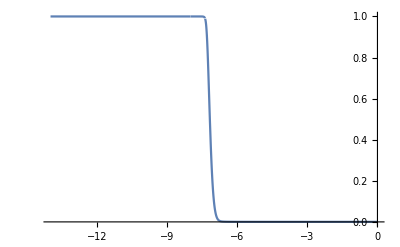

```mathematica
bxeflna=Piecewise[{{1,lna<testlnaset[[1]]},{testbxefit[lna],testlnaset[[1]]<=lna<=testlnaset[[-1]]},{bxe[lna]/.bxesol[[1]],lna>testlnaset[[-1]]}}];bxelna[lna_]=bxeflna;bganum=Exp[lna]*bxeflna*epbsollna/mhnum*sitnum/.numrep0;Plot[bxeflna,{lna,lnaini,0}]
```

```mathematica
AbsoluteTiming[npt1=1000;xsettemp=Table[lnaini+(lnaend-lnaini)/(npt1-1)*(i-1),{i,1,npt1}];ysettemp=Table[0,{i,1,npt1}];lnanpttemp=131;Do[{lna1temp,lna2temp}={xsettemp[[npt1-i]],xsettemp[[npt1-i+1]]};lnasettemp=Table[lna1temp+(lna2temp-lna1temp)/(lnanpttemp-1)*(ii-1),{ii,1,lnanpttemp}];bgasettemp=Table[bganum/calhfitlna[lna]/.lna->lnasettemp[[ii]],{ii,1,lnanpttemp}];intgtemp=Simpsonnintg[lnasettemp,bgasettemp];ysettemp[[npt1-i]]=ysettemp[[npt1-i+1]]+intgtemp,{i,1,npt1-1}]]
```

{3.18675,Null}

```mathematica
taunum=Interpolation[Table[{xsettemp[[i]],ysettemp[[i]]},{i,1,npt1}],InterpolationOrder->3,Method->"Spline"];gnum=bganum*Exp[-taunum[lna]];
```

## 5. Solve the perturbation equations numerically

```mathematica
{knummin,knummax}={0.01,1500};kcoanpt=200;knumcoaset=Table[knummin+(knummax-knummin)*(i-1)^2/(kcoanpt-1)^2,{i,1,kcoanpt}];(* knumcoaset=Table[knummin+(knummax-knummin)/(kcoanpt-1)*(i-1),{i,1,kcoanpt}]; *)lnacoanpt=1000;lna1num=-8.5;lnacoaset=Table[lna1num+(lnaend-lna1num)*(i-1)/(lnacoanpt-1),{i,1,lnacoanpt}];kpauseset={0,IntegerPart[7*kcoanpt/25],IntegerPart[11*kcoanpt/25],IntegerPart[15*kcoanpt/25],IntegerPart[19*kcoanpt/25],IntegerPart[22*kcoanpt/25],kcoanpt}
```

{0,56,88,120,152,176,200}

```mathematica
lnacoaset
```

{-8.5,-8.49149,-8.48298,-8.47447,-8.46597,-8.45746,-8.44895,-8.44044,-8.43193,-8.42342,-8.41491,-8.40641,-8.3979,-8.38939,-8.38088,-8.37237,-8.36386,-8.35536,-8.34685,-8.33834,-8.32983,-8.32132,-8.31281,-8.3043,-8.2958,-8.28729,-8.27878,-8.27027,-8.26176,-8.25325,-8.24474,-8.23624,-8.22773,-8.21922,-8.21071,-8.2022,-8.19369,-8.18519,-8.17668,-8.16817,-8.15966,-8.15115,-8.14264,-8.13413,-8.12563,-8.11712,-8.10861,-8.1001,-8.09159,-8.08308,-8.07457,-8.06607,-8.05756,-8.04905,-8.04054,-8.03203,-8.02352,-8.01502,-8.00651,-7.998,-7.98949,-7.98098,-7.97247,-7.96396,-7.95546,-7.94695,-7.93844,-7.92993,-7.92142,-7.91291,-7.9044,-7.8959,-7.88739,-7.87888,-7.87037,-7.86186,-7.85335,-7.84484,-7.83634,-7.82783,-7.81932,-7.81081,-7.8023,-7.79379,-7.78529,-7.77678,-7.76827,-7.75976,-7.75125,-7.74274,-7.73423,-7.72573,-7.71722,-7.70871,-7.7002,-7.69169,-7.68318,-7.67467,-7.66617,-7.65766,-7.64915,-7.64064,-7.63213,-7.62362,-7.61512,-7.60661,-7.5981,-7.58959,-7.58108,-7.57257,-7.56406,-7.55556,-7.54705,-7.53854,-7.53003,-7.52152,-7.51301,-7.5045,-7.496,-7.48749,-7.47898,-7.47047,-7.46196,-7.45345,-7.44494,-7.43644,-7.42793,-7.41942,-7.41091,-7.4024,-7.39389,-7.38539,-7.37688,-7.36837,-7.35986,-7.35135,-7.34284,-7.33433,-7.32583,-7.31732,-7.30881,-7.3003,-7.29179,-7.28328,-7.27477,-7.26627,-7.25776,-7.24925,-7.24074,-7.23223,-7.22372,-7.21522,-7.20671,-7.1982,-7.18969,-7.18118,-7.17267,-7.16416,-7.15566,-7.14715,-7.13864,-7.13013,-7.12162,-7.11311,-7.1046,-7.0961,-7.08759,-7.07908,-7.07057,-7.06206,-7.05355,-7.04505,-7.03654,-7.02803,-7.01952,-7.01101,-7.0025,-6.99399,-6.98549,-6.97698,-6.96847,-6.95996,-6.95145,-6.94294,-6.93443,-6.92593,-6.91742,-6.90891,-6.9004,-6.89189,-6.88338,-6.87487,-6.86637,-6.85786,-6.84935,-6.84084,-6.83233,-6.82382,-6.81532,-6.80681,-6.7983,-6.78979,-6.78128,-6.77277,-6.76426,-6.75576,-6.74725,-6.73874,-6.73023,-6.72172,-6.71321,-6.7047,-6.6962,-6.68769,-6.67918,-6.67067,-6.66216,-6.65365,-6.64515,-6.63664,-6.62813,-6.61962,-6.61111,-6.6026,-6.59409,-6.58559,-6.57708,-6.56857,-6.56006,-6.55155,-6.54304,-6.53453,-6.52603,-6.51752,-6.50901,-6.5005,-6.49199,-6.48348,-6.47497,-6.46647,-6.45796,-6.44945,-6.44094,-6.43243,-6.42392,-6.41542,-6.40691,-6.3984,-6.38989,-6.38138,-6.37287,-6.36436,-6.35586,-6.34735,-6.33884,-6.33033,-6.32182,-6.31331,-6.3048,-6.2963,-6.28779,-6.27928,-6.27077,-6.26226,-6.25375,-6.24525,-6.23674,-6.22823,-6.21972,-6.21121,-6.2027,-6.19419,-6.18569,-6.17718,-6.16867,-6.16016,-6.15165,-6.14314,-6.13463,-6.12613,-6.11762,-6.10911,-6.1006,-6.09209,-6.08358,-6.07508,-6.06657,-6.05806,-6.04955,-6.04104,-6.03253,-6.02402,-6.01552,-6.00701,-5.9985,-5.98999,-5.98148,-5.97297,-5.96446,-5.95596,-5.94745,-5.93894,-5.93043,-5.92192,-5.91341,-5.9049,-5.8964,-5.88789,-5.87938,-5.87087,-5.86236,-5.85385,-5.84535,-5.83684,-5.82833,-5.81982,-5.81131,-5.8028,-5.79429,-5.78579,-5.77728,-5.76877,-5.76026,-5.75175,-5.74324,-5.73473,-5.72623,-5.71772,-5.70921,-5.7007,-5.69219,-5.68368,-5.67518,-5.66667,-5.65816,-5.64965,-5.64114,-5.63263,-5.62412,-5.61562,-5.60711,-5.5986,-5.59009,-5.58158,-5.57307,-5.56456,-5.55606,-5.54755,-5.53904,-5.53053,-5.52202,-5.51351,-5.50501,-5.4965,-5.48799,-5.47948,-5.47097,-5.46246,-5.45395,-5.44545,-5.43694,-5.42843,-5.41992,-5.41141,-5.4029,-5.39439,-5.38589,-5.37738,-5.36887,-5.36036,-5.35185,-5.34334,-5.33483,-5.32633,-5.31782,-5.30931,-5.3008,-5.29229,-5.28378,-5.27528,-5.26677,-5.25826,-5.24975,-5.24124,-5.23273,-5.22422,-5.21572,-5.20721,-5.1987,-5.19019,-5.18168,-5.17317,-5.16466,-5.15616,-5.14765,-5.13914,-5.13063,-5.12212,-5.11361,-5.10511,-5.0966,-5.08809,-5.07958,-5.07107,-5.06256,-5.05405,-5.04555,-5.03704,-5.02853,-5.02002,-5.01151,-5.003,-4.99449,-4.98599,-4.97748,-4.96897,-4.96046,-4.95195,-4.94344,-4.93493,-4.92643,-4.91792,-4.90941,-4.9009,-4.89239,-4.88388,-4.87538,-4.86687,-4.85836,-4.84985,-4.84134,-4.83283,-4.82432,-4.81582,-4.80731,-4.7988,-4.79029,-4.78178,-4.77327,-4.76476,-4.75626,-4.74775,-4.73924,-4.73073,-4.72222,-4.71371,-4.70521,-4.6967,-4.68819,-4.67968,-4.67117,-4.66266,-4.65415,-4.64565,-4.63714,-4.62863,-4.62012,-4.61161,-4.6031,-4.59459,-4.58609,-4.57758,-4.56907,-4.56056,-4.55205,-4.54354,-4.53504,-4.52653,-4.51802,-4.50951,-4.501,-4.49249,-4.48398,-4.47548,-4.46697,-4.45846,-4.44995,-4.44144,-4.43293,-4.42442,-4.41592,-4.40741,-4.3989,-4.39039,-4.38188,-4.37337,-4.36486,-4.35636,-4.34785,-4.33934,-4.33083,-4.32232,-4.31381,-4.30531,-4.2968,-4.28829,-4.27978,-4.27127,-4.26276,-4.25425,-4.24575,-4.23724,-4.22873,-4.22022,-4.21171,-4.2032,-4.19469,-4.18619,-4.17768,-4.16917,-4.16066,-4.15215,-4.14364,-4.13514,-4.12663,-4.11812,-4.10961,-4.1011,-4.09259,-4.08408,-4.07558,-4.06707,-4.05856,-4.05005,-4.04154,-4.03303,-4.02452,-4.01602,-4.00751,-3.999,-3.99049,-3.98198,-3.97347,-3.96496,-3.95646,-3.94795,-3.93944,-3.93093,-3.92242,-3.91391,-3.90541,-3.8969,-3.88839,-3.87988,-3.87137,-3.86286,-3.85435,-3.84585,-3.83734,-3.82883,-3.82032,-3.81181,-3.8033,-3.79479,-3.78629,-3.77778,-3.76927,-3.76076,-3.75225,-3.74374,-3.73524,-3.72673,-3.71822,-3.70971,-3.7012,-3.69269,-3.68418,-3.67568,-3.66717,-3.65866,-3.65015,-3.64164,-3.63313,-3.62462,-3.61612,-3.60761,-3.5991,-3.59059,-3.58208,-3.57357,-3.56507,-3.55656,-3.54805,-3.53954,-3.53103,-3.52252,-3.51401,-3.50551,-3.497,-3.48849,-3.47998,-3.47147,-3.46296,-3.45445,-3.44595,-3.43744,-3.42893,-3.42042,-3.41191,-3.4034,-3.39489,-3.38639,-3.37788,-3.36937,-3.36086,-3.35235,-3.34384,-3.33534,-3.32683,-3.31832,-3.30981,-3.3013,-3.29279,-3.28428,-3.27578,-3.26727,-3.25876,-3.25025,-3.24174,-3.23323,-3.22472,-3.21622,-3.20771,-3.1992,-3.19069,-3.18218,-3.17367,-3.16517,-3.15666,-3.14815,-3.13964,-3.13113,-3.12262,-3.11411,-3.10561,-3.0971,-3.08859,-3.08008,-3.07157,-3.06306,-3.05455,-3.04605,-3.03754,-3.02903,-3.02052,-3.01201,-3.0035,-2.99499,-2.98649,-2.97798,-2.96947,-2.96096,-2.95245,-2.94394,-2.93544,-2.92693,-2.91842,-2.90991,-2.9014,-2.89289,-2.88438,-2.87588,-2.86737,-2.85886,-2.85035,-2.84184,-2.83333,-2.82482,-2.81632,-2.80781,-2.7993,-2.79079,-2.78228,-2.77377,-2.76527,-2.75676,-2.74825,-2.73974,-2.73123,-2.72272,-2.71421,-2.70571,-2.6972,-2.68869,-2.68018,-2.67167,-2.66316,-2.65465,-2.64615,-2.63764,-2.62913,-2.62062,-2.61211,-2.6036,-2.5951,-2.58659,-2.57808,-2.56957,-2.56106,-2.55255,-2.54404,-2.53554,-2.52703,-2.51852,-2.51001,-2.5015,-2.49299,-2.48448,-2.47598,-2.46747,-2.45896,-2.45045,-2.44194,-2.43343,-2.42492,-2.41642,-2.40791,-2.3994,-2.39089,-2.38238,-2.37387,-2.36537,-2.35686,-2.34835,-2.33984,-2.33133,-2.32282,-2.31431,-2.30581,-2.2973,-2.28879,-2.28028,-2.27177,-2.26326,-2.25475,-2.24625,-2.23774,-2.22923,-2.22072,-2.21221,-2.2037,-2.1952,-2.18669,-2.17818,-2.16967,-2.16116,-2.15265,-2.14414,-2.13564,-2.12713,-2.11862,-2.11011,-2.1016,-2.09309,-2.08458,-2.07608,-2.06757,-2.05906,-2.05055,-2.04204,-2.03353,-2.02503,-2.01652,-2.00801,-1.9995,-1.99099,-1.98248,-1.97397,-1.96547,-1.95696,-1.94845,-1.93994,-1.93143,-1.92292,-1.91441,-1.90591,-1.8974,-1.88889,-1.88038,-1.87187,-1.86336,-1.85485,-1.84635,-1.83784,-1.82933,-1.82082,-1.81231,-1.8038,-1.7953,-1.78679,-1.77828,-1.76977,-1.76126,-1.75275,-1.74424,-1.73574,-1.72723,-1.71872,-1.71021,-1.7017,-1.69319,-1.68468,-1.67618,-1.66767,-1.65916,-1.65065,-1.64214,-1.63363,-1.62513,-1.61662,-1.60811,-1.5996,-1.59109,-1.58258,-1.57407,-1.56557,-1.55706,-1.54855,-1.54004,-1.53153,-1.52302,-1.51451,-1.50601,-1.4975,-1.48899,-1.48048,-1.47197,-1.46346,-1.45495,-1.44645,-1.43794,-1.42943,-1.42092,-1.41241,-1.4039,-1.3954,-1.38689,-1.37838,-1.36987,-1.36136,-1.35285,-1.34434,-1.33584,-1.32733,-1.31882,-1.31031,-1.3018,-1.29329,-1.28478,-1.27628,-1.26777,-1.25926,-1.25075,-1.24224,-1.23373,-1.22523,-1.21672,-1.20821,-1.1997,-1.19119,-1.18268,-1.17417,-1.16567,-1.15716,-1.14865,-1.14014,-1.13163,-1.12312,-1.11461,-1.10611,-1.0976,-1.08909,-1.08058,-1.07207,-1.06356,-1.05506,-1.04655,-1.03804,-1.02953,-1.02102,-1.01251,-1.004,-0.995495,-0.986987,-0.978478,-0.96997,-0.961461,-0.952953,-0.944444,-0.935936,-0.927427,-0.918919,-0.91041,-0.901902,-0.893393,-0.884885,-0.876376,-0.867868,-0.859359,-0.850851,-0.842342,-0.833834,-0.825325,-0.816817,-0.808308,-0.7998,-0.791291,-0.782783,-0.774274,-0.765766,-0.757257,-0.748749,-0.74024,-0.731732,-0.723223,-0.714715,-0.706206,-0.697698,-0.689189,-0.680681,-0.672172,-0.663664,-0.655155,-0.646647,-0.638138,-0.62963,-0.621121,-0.612613,-0.604104,-0.595596,-0.587087,-0.578579,-0.57007,-0.561562,-0.553053,-0.544545,-0.536036,-0.527528,-0.519019,-0.510511,-0.502002,-0.493493,-0.484985,-0.476476,-0.467968,-0.459459,-0.450951,-0.442442,-0.433934,-0.425425,-0.416917,-0.408408,-0.3999,-0.391391,-0.382883,-0.374374,-0.365866,-0.357357,-0.348849,-0.34034,-0.331832,-0.323323,-0.314815,-0.306306,-0.297798,-0.289289,-0.280781,-0.272272,-0.263764,-0.255255,-0.246747,-0.238238,-0.22973,-0.221221,-0.212713,-0.204204,-0.195696,-0.187187,-0.178679,-0.17017,-0.161662,-0.153153,-0.144645,-0.136136,-0.127628,-0.119119,-0.110611,-0.102102,-0.0935936,-0.0850851,-0.0765766,-0.0680681,-0.0595596,-0.0510511,-0.0425425,-0.034034,-0.0255255,-0.017017,-0.00850851,0.}

```mathematica
kpauseind=1;If[kpauseind==1,Export[StringJoin["GR_background_data.txt"],Table[{etset[[i]],soltab[[i,1]],soltab[[i,2]],soltab[[i,3]]},{i,1,Length[etset]}],"Table"];Export[StringJoin["GR_lna_data.txt"],lnacoaset,"Table"];Export[StringJoin["GR_k_data.txt"],knumcoaset,"Table"];]
```

```mathematica
sourcedis1set=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];sourcedis2set=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];
```

```mathematica
labelsol=0;If[labelsol==0,{parbth00,parc1,parc4}={1,0,0}];If[labelsol==1,{parbth00,parc1,parc4}={0,1,0}];If[labelsol==4,{parbth00,parc1,parc4}={0,0,1}]
```

```mathematica
AbsoluteTiming[Do[knum=knumcoaset[[kcoai]];{bth00num,solc1,solc4}={parbth00,parc1,parc4}*Sqrt[decalrsq]/.k->knum;finiset={testbph,testdeb,testdec,testvb,testvc}/.grinisol3/.grinisol2/.grinisol1/.grinisol0/.gradbcon/.numrep0/.bph0->-2*bth00num/.{bga0->bxeflna*(3*Omb0num)/(8*Pi*mhnum)*sitnum,bga1->0,bga2->0}/.k->knum/.lna->lnaini/.a->aininum;bthiniset={testbth0,testbth1,testbth2}/.grinisol3/.grinisol2/.grinisol1/.grinisol0/.gradbcon/.numrep0/.bph0->-2*bth00num/.{bga0->bxeflna*(3*Omb0num)/(8*Pi*mhnum)*sitnum,bga1->0,bga2->0}/.k->knum/.lna->lnaini/.a->aininum;etininum=bumetfitlna[Log[aininum]];asep1=1;parnum=1.8;If[parnum*boln/knum>=etend,Print["1 ",{kcoai,knum,parnum*boln/knum,etend}];fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];{source1f1,source1f2}={gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a]),-gnum*vb[a]}/.numrep0/.lna->Log[a]/.bumsol[[1]]];If[etininum<parnum*boln/knum<etend,Print["2 ",{kcoai,knum,parnum*boln/knum,etend}];asep1=af[et]/.bgsol[[1]]/.et->parnum*boln/knum;fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,asep1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];fsep1set={bph[a],deb[a],dec[a],vb[a],vc[a],bthf[a,0],bthf[a,1],bthf[a,2]}/.bumsol[[1]]/.a->asep1;sep1eqnumber=8;fpsoltrsetnum=Table[fpsoltrset[[i]]/.{bthf[a,3]->5/(k*etf[a])*bthf[a,2]-bthf[a,1]}/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum,{i,1,sep1eqnumber}];ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,sep1eqnumber}]];ndsoliniset={bph[asep1]==fsep1set[[1]],deb[asep1]==fsep1set[[2]],dec[asep1]==fsep1set[[3]],vb[asep1]==fsep1set[[4]],vc[asep1]==fsep1set[[5]],bthf[asep1,0]==fsep1set[[6]],bthf[asep1,1]==fsep1set[[7]],bthf[asep1,2]==fsep1set[[8]]};ndsolfset={bph,bps,deb,dec,vb,vc,bthf[a,0],bthf[a,1],bthf[a,2]};bumsep1sol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,asep1,1},PrecisionGoal->pgnum3,"StartingStepSize"->10^-pgnum3];source1f1=Piecewise[{{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.lna->Log[a]/.bumsol[[1]],a<asep1},{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}];source1f2=Piecewise[{{-gnum*vb[a]/.numrep0/.lna->Log[a]/.bumsol[[1]],a<asep1},{-gnum*vb[a]/.numrep0/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}]];Do[{sourcedis1set[[lnai,kcoai]],sourcedis2set[[lnai,kcoai]]}={source1f1,source1f2}/.a->Exp[lnacoaset[[lnai]]],{lnai,1,lnacoanpt}],{kcoai,1,kcoanpt}]]
```

1 {1,0.01,3600.,3.25901}

General::munfl: Exp[-710.169] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1 {2,0.0478776,751.918,3.25901}

1 {3,0.16151,222.896,3.25901}

1 {4,0.350898,102.594,3.25901}

1 {5,0.616041,58.4376,3.25901}

1 {6,0.956939,37.6199,3.25901}

1 {7,1.37359,26.2086,3.25901}

1 {8,1.866,19.2926,3.25901}

1 {9,2.43417,14.7895,3.25901}

1 {10,3.07808,11.6956,3.25901}

1 {11,3.79776,9.47928,3.25901}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

1 {12,4.59319,7.8377,3.25901}

1 {13,5.46437,6.58813,3.25901}

1 {14,6.41131,5.61508,3.25901}

1 {15,7.43401,4.84261,3.25901}

1 {16,8.53246,4.21918,3.25901}

1 {17,9.70666,3.70879,3.25901}

1 {18,10.9566,3.28568,3.25901}

2 {19,12.2823,2.93104,3.25901}

2 {20,13.6838,2.63085,3.25901}

2 {21,15.161,2.37451,3.25901}

2 {22,16.714,2.15388,3.25901}

2 {23,18.3427,1.96263,3.25901}

2 {24,20.0472,1.79576,3.25901}

2 {25,21.8275,1.6493,3.25901}

2 {26,23.6835,1.52005,3.25901}

2 {27,25.6152,1.40541,3.25901}

2 {28,27.6228,1.30327,3.25901}

2 {29,29.706,1.21188,3.25901}

2 {30,31.865,1.12976,3.25901}

2 {31,34.0998,1.05572,3.25901}

2 {32,36.4104,0.98873,3.25901}

2 {33,38.7966,0.927915,3.25901}

2 {34,41.2587,0.872544,3.25901}

2 {35,43.7965,0.821984,3.25901}

2 {36,46.41,0.775694,3.25901}

2 {37,49.0993,0.733207,3.25901}

2 {38,51.8644,0.694118,3.25901}

2 {39,54.7052,0.658072,3.25901}

2 {40,57.6218,0.624764,3.25901}

2 {41,60.6141,0.593921,3.25901}

2 {42,63.6822,0.565307,3.25901}

2 {43,66.826,0.538712,3.25901}

2 {44,70.0456,0.513951,3.25901}

2 {45,73.341,0.490858,3.25901}

2 {46,76.7121,0.469287,3.25901}

2 {47,80.159,0.449108,3.25901}

2 {48,83.6816,0.430202,3.25901}

2 {49,87.2799,0.412466,3.25901}

2 {50,90.9541,0.395804,3.25901}

2 {51,94.7039,0.380132,3.25901}

2 {52,98.5296,0.365373,3.25901}

2 {53,102.431,0.351456,3.25901}

2 {54,106.408,0.33832,3.25901}

2 {55,110.461,0.325907,3.25901}

2 {56,114.59,0.314164,3.25901}

2 {57,118.794,0.303045,3.25901}

2 {58,123.074,0.292506,3.25901}

2 {59,127.43,0.282508,3.25901}

2 {60,131.862,0.273013,3.25901}

2 {61,136.369,0.263989,3.25901}

2 {62,140.952,0.255405,3.25901}

2 {63,145.611,0.247233,3.25901}

2 {64,150.346,0.239447,3.25901}

2 {65,155.157,0.232024,3.25901}

2 {66,160.043,0.22494,3.25901}

2 {67,165.005,0.218176,3.25901}

2 {68,170.042,0.211712,3.25901}

2 {69,175.156,0.205531,3.25901}

2 {70,180.345,0.199617,3.25901}

2 {71,185.61,0.193955,3.25901}

2 {72,190.951,0.18853,3.25901}

2 {73,196.367,0.18333,3.25901}

2 {74,201.86,0.178342,3.25901}

2 {75,207.428,0.173555,3.25901}

2 {76,213.071,0.168957,3.25901}

2 {77,218.791,0.164541,3.25901}

2 {78,224.586,0.160295,3.25901}

2 {79,230.457,0.156211,3.25901}

2 {80,236.404,0.152282,3.25901}

2 {81,242.427,0.148499,3.25901}

2 {82,248.525,0.144855,3.25901}

2 {83,254.699,0.141343,3.25901}

2 {84,260.949,0.137958,3.25901}

2 {85,267.274,0.134693,3.25901}

2 {86,273.676,0.131543,3.25901}

2 {87,280.153,0.128501,3.25901}

2 {88,286.705,0.125564,3.25901}

2 {89,293.334,0.122727,3.25901}

2 {90,300.038,0.119985,3.25901}

2 {91,306.818,0.117333,3.25901}

2 {92,313.674,0.114769,3.25901}

2 {93,320.606,0.112287,3.25901}

2 {94,327.613,0.109886,3.25901}

2 {95,334.696,0.10756,3.25901}

2 {96,341.855,0.105308,3.25901}

2 {97,349.09,0.103125,3.25901}

2 {98,356.4,0.10101,3.25901}

2 {99,363.786,0.0989592,3.25901}

2 {100,371.248,0.0969702,3.25901}

2 {101,378.786,0.0950405,3.25901}

2 {102,386.399,0.0931679,3.25901}

2 {103,394.088,0.0913501,3.25901}

2 {104,401.853,0.0895849,3.25901}

2 {105,409.694,0.0878705,3.25901}

2 {106,417.61,0.0862048,3.25901}

2 {107,425.602,0.084586,3.25901}

2 {108,433.67,0.0830124,3.25901}

2 {109,441.814,0.0814822,3.25901}

2 {110,450.034,0.079994,3.25901}

2 {111,458.329,0.0785462,3.25901}

2 {112,466.7,0.0771374,3.25901}

2 {113,475.146,0.0757661,3.25901}

2 {114,483.669,0.0744311,3.25901}

2 {115,492.267,0.073131,3.25901}

2 {116,500.941,0.0718648,3.25901}

2 {117,509.691,0.0706311,3.25901}

2 {118,518.516,0.0694289,3.25901}

2 {119,527.417,0.0682571,3.25901}

2 {120,536.394,0.0671148,3.25901}

2 {121,545.447,0.0660009,3.25901}

2 {122,554.576,0.0649145,3.25901}

2 {123,563.78,0.0638547,3.25901}

2 {124,573.06,0.0628207,3.25901}

2 {125,582.416,0.0618115,3.25901}

2 {126,591.847,0.0608265,3.25901}

2 {127,601.354,0.0598649,3.25901}

2 {128,610.937,0.0589258,3.25901}

2 {129,620.596,0.0580087,3.25901}

2 {130,630.331,0.0571129,3.25901}

2 {131,640.141,0.0562376,3.25901}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

2 {132,650.027,0.0553823,3.25901}

2 {133,659.989,0.0545464,3.25901}

2 {134,670.026,0.0537292,3.25901}

2 {135,680.14,0.0529303,3.25901}

2 {136,690.329,0.0521491,3.25901}

2 {137,700.594,0.051385,3.25901}

2 {138,710.934,0.0506376,3.25901}

2 {139,721.351,0.0499064,3.25901}

2 {140,731.843,0.0491909,3.25901}

2 {141,742.411,0.0484907,3.25901}

2 {142,753.054,0.0478053,3.25901}

2 {143,763.773,0.0471344,3.25901}

2 {144,774.569,0.0464775,3.25901}

2 {145,785.439,0.0458342,3.25901}

2 {146,796.386,0.0452042,3.25901}

2 {147,807.408,0.0445871,3.25901}

2 {148,818.507,0.0439825,3.25901}

2 {149,829.68,0.0433902,3.25901}

2 {150,840.93,0.0428097,3.25901}

2 {151,852.256,0.0422409,3.25901}

2 {152,863.657,0.0416832,3.25901}

2 {153,875.134,0.0411366,3.25901}

2 {154,886.686,0.0406006,3.25901}

2 {155,898.315,0.040075,3.25901}

2 {156,910.019,0.0395596,3.25901}

2 {157,921.799,0.0390541,3.25901}

2 {158,933.654,0.0385582,3.25901}

2 {159,945.586,0.0380716,3.25901}

2 {160,957.593,0.0375943,3.25901}

2 {161,969.676,0.0371258,3.25901}

2 {162,981.835,0.036666,3.25901}

2 {163,994.069,0.0362148,3.25901}

2 {164,1006.38,0.0357718,3.25901}

2 {165,1018.77,0.0353369,3.25901}

2 {166,1031.23,0.0349099,3.25901}

2 {167,1043.76,0.0344905,3.25901}

2 {168,1056.38,0.0340787,3.25901}

2 {169,1069.07,0.0336742,3.25901}

2 {170,1081.83,0.0332769,3.25901}

2 {171,1094.67,0.0328866,3.25901}

2 {172,1107.59,0.0325031,3.25901}

2 {173,1120.58,0.0321262,3.25901}

2 {174,1133.65,0.0317559,3.25901}

2 {175,1146.79,0.0313919,3.25901}

2 {176,1160.01,0.0310342,3.25901}

2 {177,1173.31,0.0306825,3.25901}

2 {178,1186.68,0.0303368,3.25901}

2 {179,1200.12,0.0299969,3.25901}

2 {180,1213.65,0.0296627,3.25901}

2 {181,1227.24,0.029334,3.25901}

2 {182,1240.92,0.0290108,3.25901}

2 {183,1254.67,0.0286929,3.25901}

2 {184,1268.49,0.0283802,3.25901}

2 {185,1282.39,0.0280725,3.25901}

2 {186,1296.37,0.0277698,3.25901}

2 {187,1310.42,0.0274721,3.25901}

2 {188,1324.55,0.027179,3.25901}

2 {189,1338.76,0.0268907,3.25901}

2 {190,1353.03,0.0266069,3.25901}

2 {191,1367.39,0.0263275,3.25901}

2 {192,1381.82,0.0260526,3.25901}

2 {193,1396.33,0.0257819,3.25901}

2 {194,1410.91,0.0255154,3.25901}

2 {195,1425.57,0.025253,3.25901}

2 {196,1440.3,0.0249947,3.25901}

2 {197,1455.12,0.0247403,3.25901}

2 {198,1470.,0.0244898,3.25901}

2 {199,1484.96,0.024243,3.25901}

2 {200,1500.,0.024,3.25901}

{570.096,Null}

```mathematica
knum=knumcoaset[[100]];{bth00num,solc1,solc4}={parbth00,parc1,parc4}*Sqrt[decalrsq]/.k->knum;finiset={testbph,testdeb,testdec,testvb,testvc}/.grinisol3/.grinisol2/.grinisol1/.grinisol0/.gradbcon/.numrep0/.bph0->-2*bth00num/.{bga0->bxeflna*(3*Omb0num)/(8*Pi*mhnum)*sitnum,bga1->0,bga2->0}/.k->knum/.lna->lnaini/.a->aininum;bthiniset={testbth0,testbth1,testbth2}/.grinisol3/.grinisol2/.grinisol1/.grinisol0/.gradbcon/.numrep0/.bph0->-2*bth00num/.{bga0->bxeflna*(3*Omb0num)/(8*Pi*mhnum)*sitnum,bga1->0,bga2->0}/.k->knum/.lna->lnaini/.a->aininum;etininum=bumetfitlna[Log[aininum]];asep1=1;parnum=1.8;If[parnum*boln/knum>=etend,Print["1 ",{kcoai,knum,parnum*boln/knum,etend}];fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];{source1f1,source1f2}={gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a]),-gnum*vb[a]}/.numrep0/.lna->Log[a]/.bumsol[[1]]];If[etininum<parnum*boln/knum<etend,Print["2 ",{kcoai,knum,parnum*boln/knum,etend}];asep1=af[et]/.bgsol[[1]]/.et->parnum*boln/knum;fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,asep1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];fsep1set={bph[a],deb[a],dec[a],vb[a],vc[a],bthf[a,0],bthf[a,1],bthf[a,2]}/.bumsol[[1]]/.a->asep1;sep1eqnumber=8;fpsoltrsetnum=Table[fpsoltrset[[i]]/.{bthf[a,3]->5/(k*etf[a])*bthf[a,2]-bthf[a,1]}/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum,{i,1,sep1eqnumber}];ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,sep1eqnumber}]];ndsoliniset={bph[asep1]==fsep1set[[1]],deb[asep1]==fsep1set[[2]],dec[asep1]==fsep1set[[3]],vb[asep1]==fsep1set[[4]],vc[asep1]==fsep1set[[5]],bthf[asep1,0]==fsep1set[[6]],bthf[asep1,1]==fsep1set[[7]],bthf[asep1,2]==fsep1set[[8]]};ndsolfset={bph,bps,deb,dec,vb,vc,bthf[a,0],bthf[a,1],bthf[a,2]};bumsep1sol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,asep1,1},PrecisionGoal->pgnum3,"StartingStepSize"->10^-pgnum3];source1f1=Piecewise[{{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.lna->Log[a]/.bumsol[[1]],a<asep1},{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}];source1f2=Piecewise[{{-gnum*vb[a]/.numrep0/.lna->Log[a]/.bumsol[[1]],a<asep1},{-gnum*vb[a]/.numrep0/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}]];testdata=Table[{source1f1,source1f2}/.a->Exp[lnacoaset[[lnai]]],{lnai,1,lnacoanpt}];
```

2 {kcoai,371.248,0.0969702,3.25901}

General::munfl: Exp[-710.169] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
bph[a]/2/.bumsol[[1]]/.a->aininum
```

-0.999616

```mathematica
bph[a]/2/.bumsol[[1]]/.a->Exp[lnacoaset[[100]]]
```

-0.179712

```mathematica
testdata[[500]]/2
```

{0.00896201,-0.0164443}

```mathematica
sourcedis2set[[10,500]]
```

Part::partw: Part 500 of {-6.00165×10^-268,0,0,0,0,0,0,0,0,0,«190»} does not exist.

```mathematica
sourcedis1setflat=Flatten[Table[{{lnacoaset[[ii]],knumcoaset[[kk]]},sourcedis1set[[ii,kk]]},{ii,1,Length[lnacoaset]},{kk,1,Length[knumcoaset]}],1];source1fit=Interpolation[sourcedis1setflat,Method->"Spline",InterpolationOrder->3];
```

```mathematica
Plot3D[source1fit[x,y],{x,lnacoaset[[1]],lnacoaset[[-1]]},{y,knumcoaset[[1]],knumcoaset[[-1]]},PlotRange->All]
```

-Graphics3D-

```mathematica
AbsoluteTiming[Export[StringJoin["GR_sourcedis1set_data.txt"],sourcedis1set,"Table"];Export[StringJoin["GR_sourcedis2set_data.txt"],sourcedis2set,"Table"];]
```

{2.08617,Null}

## 6. Print total time used

```mathematica
Print["End: ",TimeUsed[]]
```

End: 1592.72